# Wolfram Quantum Framework

### WQF

Install:

```mathematica
PacletInstall["Wolfram/QuantumFramework"(*->"1.0.27"*)]
```

PacletObject[…]

Development version:

```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Load:

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
Names["Quantum*"]//Column
```

QuantumBasis
QuantumChannel
QuantumCircuitOperator
QuantumDiagramProcess
QuantumDistance
QuantumEntangledQ
QuantumEntanglementMonotone
QuantumMeasurement
QuantumMeasurementOperator
QuantumOperator
QuantumPartialTrace
QuantumPartialTranspose
QuantumState
QuantumTensorProduct
QuantumWignerTransform

Online documentation:

```mathematica
SystemOpen@"https://wolfr.am/wolfram-quantum"
```

#### QuantumBasis

```mathematica
QuantumBasis[]
%["Association"]
```

QuantumBasis[…]

<|0→{1,0},1→{0,1}|>

```mathematica
QuantumBasis["PauliX"]
```

QuantumBasis[…]

```mathematica
QuantumBasis[]["Properties"]//Short
```

{Association,ConjugateTranspose,Diagram,Dimension,«65»,TensorRepresentation,Transpose,Type}

```mathematica
QuantumBasis[]["Association"]
```

<|0→{1,0},1→{0,1}|>

```mathematica
Table[QuantumBasis[b]["Association"],{b,{"X","Y","Z"}}]//Column
```

<|ψ_(x_-)→{-1/(√2),1/(√2)},ψ_(x_+)→{1/(√2),1/(√2)}|>
<|ψ_(y_-)→{ⅈ/(√2),1/(√2)},ψ_(y_+)→{-ⅈ/(√2),1/(√2)}|>
<|ψ_(z_-)→{0,1},ψ_(z_+)→{1,0}|>

```mathematica
Normal/@QuantumBasis[<|"up"->{-1,1},"down"->{a,b}|>]["Association"]
```

<|up→{-1,1},down→{a,b}|>

```mathematica
QuantumBasis["Computational"]==QuantumBasis[]==QuantumBasis[2]
```

True

```mathematica
QuantumBasis[9]
```

QuantumBasis[…]

```mathematica
QuantumBasis[{3,3}]
```

QuantumBasis[…]

```mathematica
QuantumBasis[1]
```

QuantumBasis[…]

```mathematica
QuantumBasis[0]
```

QuantumBasis[…]

#### QuantumState

```mathematica
QuantumState[]
```

QuantumState[…]

```mathematica
QuantumState[]//TraditionalForm
```

0

Cmd+Shift+T - traditional form

```mathematica
QuantumState[]
```

0

```mathematica
QuantumState[]["Dagger"]
```

0

Symbolic:

```mathematica
QuantumState[{a,b}]
```

QuantumState[…]

```mathematica
QuantumState[{a,b}]["Amplitudes"]
```

<|0→a,1→b|>

```mathematica
x QuantumState[{a,b}]+y QuantumState[{c,d}]
```

QuantumState[…]

```mathematica
QuantumState[{a,b}]["Properties"]//Short
```

{Amplitudes,Association,Basis,Bend,«128»,Unpurify,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumState[{a,b}]["SchmidtBasis"]
```

QuantumState[…]

```mathematica
QuantumState[{a,b}]["SchmidtBasis"]==QuantumState[{a,b}]["SpectralBasis"]==QuantumState[{a,b}]["PrimeBasis"]
```

True

```mathematica
QuantumState[{"RandomPure",2}]["SchmidtBasis"]["Association"]
```

<|u_1 v_1→{{0.0508175-0.383767 ⅈ,-0.41434+0.362152 ⅈ},{0.159801-0.394519 ⅈ,-0.540814+0.27138 ⅈ}},u_1 v_2→{{0.447624+0.320101 ⅈ,0.0879317+0.376998 ⅈ},{0.388321+0.464041 ⅈ,-0.0102396+0.425531 ⅈ}},u_2 v_1→{{-0.0558764+0.421971 ⅈ,0.455588-0.398205 ⅈ},{0.145333-0.3588 ⅈ,-0.49185+0.24681 ⅈ}},u_2 v_2→{{-0.492185-0.351967 ⅈ,-0.0966853-0.414528 ⅈ},{0.353164+0.422028 ⅈ,-0.00931255+0.387005 ⅈ}}|>

```mathematica
QuantumState[{"RandomPure",3}]["SchmidtBasis"]["Association"]
```

<|u_1 v_1→{{-0.23706+0.298431 ⅈ,0.0303584-0.273327 ⅈ,0.348815-0.183381 ⅈ,-0.131906-0.417352 ⅈ},{0.0463005+0.329299 ⅈ,-0.154644-0.183466 ⅈ,0.093635-0.330846 ⅈ,-0.343263-0.167383 ⅈ}},u_1 v_2→{{-0.291029+0.159673 ⅈ,-0.0428521+0.582115 ⅈ,0.227547-0.185642 ⅈ,-0.0216088+0.173713 ⅈ},{-0.0739031+0.280046 ⅈ,0.342455+0.376942 ⅈ,0.0193252-0.255498 ⅈ,0.0968935+0.118066 ⅈ}},u_1 v_3→{{0.474047-0.0237159 ⅈ,0.0630797+0.00425474 ⅈ,0.559029+0.0530822 ⅈ,0.0402654+0.146757 ⅈ},{0.26989-0.314104 ⅈ,0.0406007-0.0373431 ⅈ,0.36954-0.321705 ⅈ,0.117027+0.062728 ⅈ}},u_1 v_4→{{0.081543+0.283525 ⅈ,-0.380102-0.0545282 ⅈ,-0.0432331-0.0950202 ⅈ,0.567714-0.00933018 ⅈ},{0.228345+0.118813 ⅈ,-0.262923+0.207658 ⅈ,-0.0860857-0.0297584 ⅈ,0.335281-0.364707 ⅈ}},u_2 v_1→{{-0.206837+0.260384 ⅈ,0.026488-0.23848 ⅈ,0.304345-0.160001 ⅈ,-0.11509-0.364144 ⅈ},{-0.0530659-0.377416 ⅈ,0.177241+0.210274 ⅈ,-0.107317+0.379188 ⅈ,0.39342+0.191841 ⅈ}},u_2 v_2→{{-0.253926+0.139316 ⅈ,-0.0373889+0.507901 ⅈ,0.198537-0.161975 ⅈ,-0.0188539+0.151567 ⅈ},{0.0847018-0.320966 ⅈ,-0.392494-0.432021 ⅈ,-0.0221489+0.292831 ⅈ,-0.111051-0.135318 ⅈ}},u_2 v_3→{{0.413611-0.0206924 ⅈ,0.0550377+0.0037123 ⅈ,0.487759+0.0463147 ⅈ,0.035132+0.128047 ⅈ},{-0.309326+0.360001 ⅈ,-0.0465332+0.0427997 ⅈ,-0.423537+0.368712 ⅈ,-0.134127-0.0718937 ⅈ}},u_2 v_4→{{0.0711471+0.247378 ⅈ,-0.331643-0.0475764 ⅈ,-0.0377213-0.082906 ⅈ,0.495336-0.00814067 ⅈ},{-0.26171-0.136174 ⅈ,0.301341-0.238001 ⅈ,0.0986645+0.0341067 ⅈ,-0.384272+0.417997 ⅈ}}|>

```mathematica
QuantumState[{{a,b},{c,d}}]
```

QuantumState[…]

```mathematica
state=QuantumState[{"RandomMixed",2},3]
```

QuantumState[…]

```mathematica
state["Purify"]
```

QuantumState[…]

```mathematica
QuantumPartialTrace[state["Purify"],{3,4}]==state==state["Purify"]["Unpurify"]
```

True

```mathematica
state=QuantumState["RandomPure",6]
```

QuantumState[…]

```mathematica
state["Bipartition"]
```

QuantumState[…]

```mathematica
state["Bipartition",2]
```

QuantumState[…]

```mathematica
state["Bipartition",2]["Transpose",{2}]
```

QuantumState[…]

```mathematica
QuantumState["RandomMixed"]["BlochPlot"]
```

-Graphics3D-

```mathematica
QuantumState[QuantumState["Plus","X"],"Y"]
```

(1/2-ⅈ/2) ψ_(y_-)+(1/2+ⅈ/2) ψ_(y_+)

```mathematica
QuantumState[QuantumState["Plus","X"],"Y"]==QuantumState["Plus"]
```

True

#### QuantumOperator

```mathematica
QuantumState["+"]["Operator"]
```

QuantumOperator[…]

```mathematica
QuantumState["+"]["Operator"]
```

00/2+01/2+10/2+11/2

```mathematica
QuantumOperator[{{1,2},{3,4}}]
```

00+2 01+3 10+4 11

```mathematica
QuantumOperator[{{1,2,3},{3,4,5}}]
```

0000+2 0010+3 0100+3 0110+4 0200+5 0210

```mathematica
QuantumOperator["Fourier"]
```

QuantumOperator[…]

```mathematica
QuantumOperator[{"Fourier",3}]
```

00/(√3)+01/(√3)+02/(√3)+10/(√3)+(ⅇ^((2 ⅈ π)/3) 11)/(√3)+(ⅇ^(-(2 ⅈ π)/3) 12)/(√3)+20/(√3)+(ⅇ^(-(2 ⅈ π)/3) 21)/(√3)+(ⅇ^((2 ⅈ π)/3) 22)/(√3)

```mathematica
QuantumOperator["Fourier"]==QuantumOperator["H"]
```

True

```mathematica
QuantumOperator["H",{3}]
```

QuantumOperator[…]

```mathematica
QuantumOperator["H",{3}]["CircuitDiagram"]
```

-Graphics-

```mathematica
QuantumCircuitOperator["Bell"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumOperator["H"]["Diagram"]
```

-Graphics-

```mathematica
QuantumCircuitOperator@QuantumOperator["CNOT"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator@QuantumOperator[{"C","NOT",{2}}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator@QuantumOperator["CNOT",{2,1}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumOperator["RandomUnitary"]["Properties"]//Short
```

{Amplitudes,Arity,Association,Basis,«168»,VectorState,VonNeumannEntropy,Weights}

```mathematica
QuantumOperator["X","ParameterSpec"->t]
```

QuantumOperator[…]

```mathematica
QuantumOperator["X","ParameterSpec"->t]["EvolutionOperator"]
```

QuantumOperator[…]

```mathematica
Exp[-I t QuantumOperator["X","ParameterSpec"->t]]["Simplify"]
```

QuantumOperator[…]

```mathematica
Exp[-I t QuantumOperator["X","ParameterSpec"->t]]["Formula"]//FullSimplify
```

Cos[t] (00+11)-ⅈ (01+10) Sin[t]

```mathematica
Exp[-I t QuantumOperator["RandomUnitary"]]
```

QuantumOperator[…]

```mathematica
QuantumOperator[QuantumOperator["RandomUnitary"],{2},{1}]
```

QuantumOperator[…]

#### Measurement

```mathematica
QuantumMeasurementOperator[]
```

QuantumMeasurementOperator[…]

```mathematica
QuantumMeasurementOperator[]@QuantumState["RandomPure"]
```

QuantumMeasurement[…]

```mathematica
m=QuantumMeasurementOperator[2->{a,b}]@QuantumState["RandomPure"]
```

QuantumMeasurement[…]

```mathematica
m["Probabilities"]
```

<|0→0.817938,1→0.182062|>

```mathematica
m["State"]
```

(0.899371+0.095236 ⅈ) a0-(0.0241824+0.426001 ⅈ) b1

```mathematica
m["Mean"]
```

0.817938 a+0.182062 b

```mathematica
s=QuantumState[{"RandomPure",2}]
```

QuantumState[…]

```mathematica
m1=QuantumMeasurementOperator[{2}]@s
```

QuantumMeasurement[…]

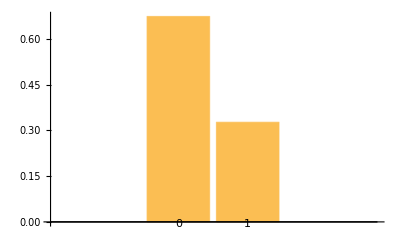

```mathematica
m1["ProbabilityPlot"]
```

```mathematica
m2=QuantumMeasurementOperator[{1,2}]@s
```

QuantumMeasurement[…]

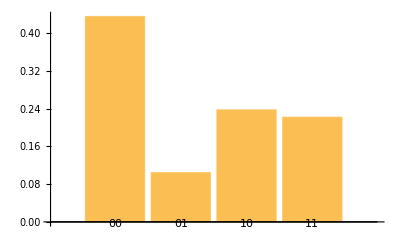

```mathematica
m2["ProbabilityPlot"]
```

```mathematica
m3=QuantumMeasurementOperator[QuantumBasis[{"X","Y"}],{1,2}]@s
```

QuantumMeasurement[…]

```mathematica
m3["Probabilities"]
```

<|ψ_(x_-)ψ_(y_-)→0.159072,ψ_(x_-)ψ_(y_+)→0.128568,ψ_(x_+)ψ_(y_-)→0.546818,ψ_(x_+)ψ_(y_+)→0.165541|>

```mathematica
m4=QuantumMeasurementOperator[{1,2}]@QuantumState[{a,b,c,d}]
```

QuantumMeasurement[…]

```mathematica
m4["Probabilities"]
```

<|00→Re[(a Conjugate[a])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])],01→Re[(b Conjugate[b])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])],10→Re[(c Conjugate[c])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])],11→Re[(d Conjugate[d])/(a Conjugate[a]+b Conjugate[b]+c Conjugate[c]+d Conjugate[d])]|>

```mathematica
TraditionalForm/@m4["StateAssociation"]
```

<|00→a 00,01→b 01,10→c 10,11→d 11|>

#### QuantumCircuitOperator

```mathematica
QuantumCircuitOperator["Toffoli"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator["Toffoli"]["Operators"]
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

```mathematica
QuantumCircuitOperator["Toffoli"][QuantumState["110"]]["Simplify"]
```

111

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["CNOT",{1,2}]}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator["Bell"]
```

QuantumCircuitOperator[…]

```mathematica
QuantumState[{"Register",2}]==QuantumState["00"]
```

True

```mathematica
QuantumCircuitOperator["Bell"][QuantumState[{"Register",2}]]
```

QuantumState[…]

```mathematica
QuantumCircuitOperator["Bell"][QuantumState[{"Register",2}]]==QuantumState["Bell"]
```

True

```mathematica
QuantumCircuitOperator["Bell"]
```

QuantumCircuitOperator[…]

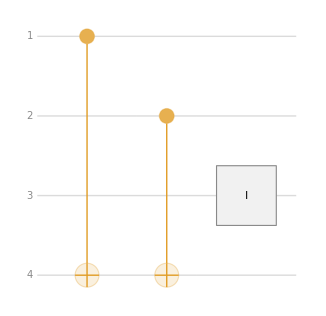

```mathematica
QuantumCircuitOperator[{"BernsteinVaziraniOracle","110"}]["Diagram"]
```

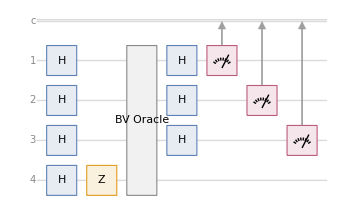

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","110"}]["Diagram","SubcircuitLevel"->0]
```

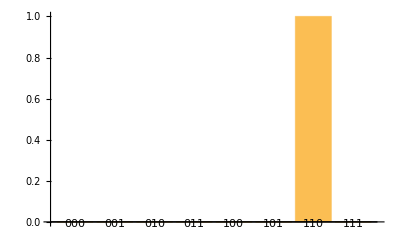

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","110"}][]["ProbabilityPlot"]
```

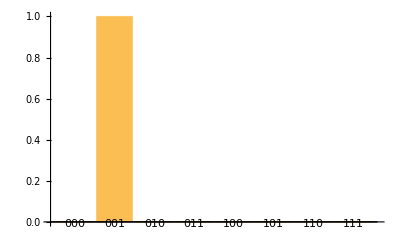

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","001"}][]["ProbabilityPlot"]
```

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&c}]
```

QuantumCircuitOperator[…]

```mathematica
SatisfiabilityInstances[a&&b&&!c,{a,b,c},All]
```

{{True,True,False}}

```mathematica
QuantumCircuitOperator[{"PhaseOracle",a&&b&&!c}][QuantumState["110"]]
```

-110

```mathematica
QuantumCircuitOperator[{"PhaseOracle",a&&b&&!c}][QuantumState["001"]]
```

001

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&!c}]@QuantumState["1100"]
```

1101

```mathematica
QuantumCircuitOperator[{"BooleanOracle",a&&b&&!c}]@QuantumState["0010"]
```

0010

```mathematica
QuantumCircuitOperator[{"Grover",a&&b&&!c}]
```

QuantumCircuitOperator[…]

```mathematica
m=(QuantumCircuitOperator[{"GroverPhase",a&&b&&!c}]/*QuantumMeasurementOperator[{1,2,3}])[QuantumState[{"UniformSuperposition",3}]]
```

QuantumMeasurement[…]

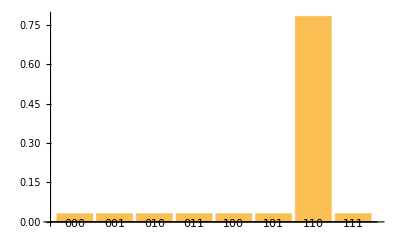

```mathematica
m["Canonical"]["ProbabilityPlot"]
```

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["X"]]
```

0001/(√2)+0011/(√2)+0100/(√2)+0110/(√2)+1001/(√2)-1011/(√2)+1100/(√2)-1110/(√2)

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["X",{2}]}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumCircuitOperator[{QuantumOperator["H"],QuantumOperator["X",{2}]}]["QuantumOperator"]
```

QuantumOperator[…]

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["X",{3}]]
```

QuantumOperator[…]

```mathematica
QuantumTensorProduct[QuantumOperator["H"],QuantumOperator["I"],QuantumOperator["X"]]
```

QuantumOperator[…]

```mathematica
QuantumOperator["RandomUnitary"]
```

QuantumOperator[…]

```mathematica
List@@QuantumOperator["RandomUnitary"]
```

{QuantumState[…],{{1},{1}}}

```mathematica
List@@QuantumMeasurementOperator[]
```

{QuantumOperator[…],{1}}

```mathematica
List@@QuantumMeasurement[…]
```

{QuantumMeasurementOperator[…]}

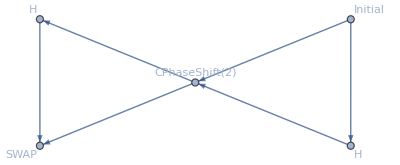

```mathematica
QuantumCircuitOperator["Fourier"]["TensorNetwork"]
```

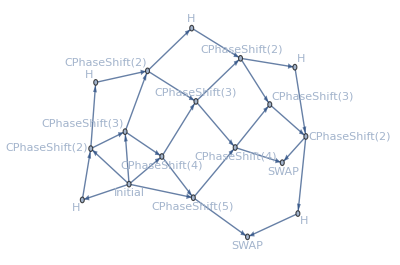

```mathematica
QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"]
```

```mathematica
QuantumCircuitOperator[{"Fourier",5}]
```

QuantumCircuitOperator[…]

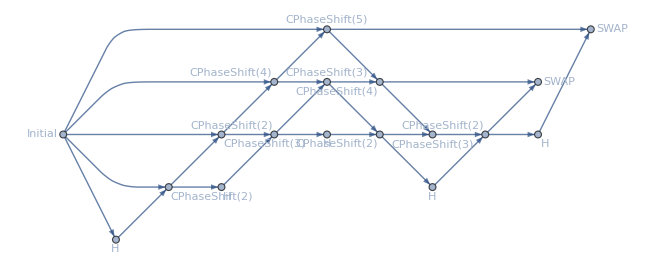

```mathematica
Graph[QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

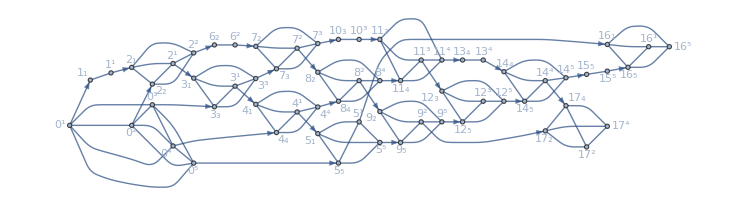

```mathematica
Graph[TensorNetworkIndexGraph@QuantumCircuitOperator[{"Fourier",5}]["TensorNetwork"],
GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

```mathematica
QuantumCircuitOperator[{"PhaseEstimation",QuantumOperator["RandomUnitary"]}]
```

QuantumCircuitOperator[…]

```mathematica
qiskit=QuantumCircuitOperator[{"BernsteinVazirani","0101"}]["Qiskit"]
```

QiskitCircuit[…]

```mathematica
measurement=qiskit[QuantumState["00000"]]
```

QuantumMeasurement[…]

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","0101"}][QuantumState["00000"],Method->"Qiskit"]
```

QuantumMeasurement[…]

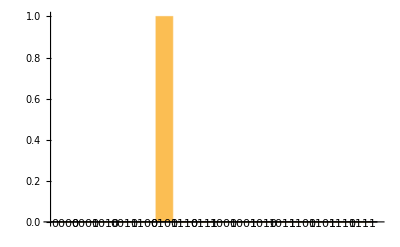

```mathematica
measurement["ProbabilityPlot"]
```

```mathematica
measurement=qiskit[QuantumState["00000"],"Provider"->"IBMQ"]
```

QuantumMeasurement[…]

```mathematica
qiskit["QASM"]
```

OPENQASM 2.0;
include "qelib1.inc";
gate i p0 {
	u3(0,0,0) p0;
}
qreg q[5];
creg c[4];
h q[0];
h q[1];
h q[2];
h q[3];
h q[4];
z q[4];
i q[0];
cx q[1],q[4];
i q[2];
cx q[3],q[4];
h q[0];
h q[1];
h q[2];
h q[3];
measure q[0] -> c[3];
measure q[1] -> c[2];
measure q[2] -> c[1];
measure q[3] -> c[0];

```mathematica
QuantumCircuitOperator[{"BernsteinVazirani","0101"}]["QASM"]
```

OPENQASM 3.0;
qubit[5] q;
bit[4] c;
U(pi/2, 0, pi) q[0];
U(pi/2, 0, pi) q[1];
U(pi/2, 0, pi) q[2];
U(pi/2, 0, pi) q[3];
U(pi/2, 0, pi) q[4];
U(0, 0, pi) q[4];
U(0, 0, pi) q[0];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[1] q[4];
U(0, 0, pi) q[2];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[3] q[4];
U(pi/2, 0, pi) q[0];
U(pi/2, 0, pi) q[1];
U(pi/2, 0, pi) q[2];
U(pi/2, 0, pi) q[3];
c[0] = measure q[0];
c[0] = measure q[1];
c[0] = measure q[2];
c[0] = measure q[3];

```mathematica
ResourceFunction["PythonVersion"][]
```

Python 3.9.1

```mathematica
ResourceFunction["PythonPackageInformation"]["qiskit"]["Version"]
```

0.36.1

Questions please: quantum@wolfram.com

```mathematica
CloudPublish[EvaluationNotebook[],"WTC22_QF_Demo.nb",Permissions->"Public"]
```